Your Title Here

```mathematica
(*SATURATION DATA*)
```

```mathematica
SHL={{1.15,359.91},{1.90,658.77},{2.16,773.78},{2.33,852.97},{2.46,915.37},{2.57,967.8},{2.66,1013.6},{2.73,1054.5},{2.8,1091.8},{2.87,1126.3},{2.93,1158.4},{2.98,1188.6},{3.03,1217.3},{3.08,1244.6},{3.13,1270.7},{3.17,1295.9},{3.21,1320.2},{3.25,1343.7},{3.29,1366.6},{3.33,1388.9},{3.36,1410.7},{3.4,1432.},{3.43,1452.9},{3.47,1473.6},{3.5,1493.9},{3.53,1514.},{3.56,1533.9},{3.6,1553.7},{3.63,1573.3},{3.66,1592.9},{3.69,1612.6},{3.72,1632.2},{3.75,1652.1},{3.78,1672.1},{3.81,1692.5},{3.84,1713.3},{3.88,1734.7},{3.91,1756.8},{3.94,1780.},{3.98,1804.4},{4.02,1830.4},{4.06,1858.9},{4.11,1891.9},{4.18,1935.9},{4.36,2055.6},{4.46,2115.7},{4.7,2274.6}(*{4.58,2195}*)};
```

```mathematica
SHV={{9.155,2500.9},{7.69,2633.3},{7.53,2652.9},{6.78,2753.1},{6.56,2779.3},{6.43,2792.1},{6.33,2798.9},{6.25,2802.2},{6.18,2803.2},{6.12,2802.5},{6.06,2800.5},{6.01,2797.5},{5.97,2793.7},{5.93,2789.1},{5.89,2783.9},{5.85,2778.2},{5.81,2771.8},{5.78,2765.},{5.74,2757.8},{5.71,2750.1},{5.68,2741.9},{5.64,2733.4},{5.61,2724.4},{5.58,2715.},{5.55,2705.1},{5.52,2694.9},{5.49,2684.1},{5.46,2672.9},{5.43,2661.3},{5.4,2649.},{5.37,2636.3},{5.34,2623.},{5.31,2609.},{5.27,2594.3},{5.24,2578.9},{5.21,2562.6},{5.17,2545.4},{5.14,2527.},{5.10,2507.4},{5.06,2486.2},{5.02,2463.1},{4.98,2437.6},{4.93,2408.7},{4.87,2374.9},{4.8,2333.},{4.7,2274.6},{4.46,2115.7}(*,{4.36,2055.6}*)};
```

```mathematica
Quiet@Interpolation[SHV,InterpolationOrder->1][(4.7+4.46)/2]
```

2195.15

```mathematica
(4.7+4.46)/2
```

4.58

```mathematica
diagram=ListPlot[{SHL,SHV},Joined->True,PlotStyle->{{Thick,Black}},PlotRange->{{4,9},{1500,3500}},PlotRangePadding->None,
Frame->True,FrameLabel->{"entropy (kJ/[kg K])","enthalpy (kJ/kg)"},LabelStyle->{17,Black},ImageSize->{600,475},AspectRatio->Full];
```

```mathematica
(*QUALITY*)
```

```mathematica
Q90={{8.3545,2286.801},(*{7.111000000000001,2435.847},*){6.993,2464.9880000000003},{6.335,2563.087},{6.1499999999999995,2592.907},{6.044,2609.67},{5.963,2620.3700000000003},{5.898,2627.43},{5.8420000000000005,2632.06},{5.795,2634.88},{5.747,2636.2900000000004},{5.707,2636.61},{5.676,2636.06},{5.645,2634.65},{5.614,2632.5800000000004},{5.582,2629.9700000000003},{5.55,2626.6400000000003},{5.527,2622.87},{5.495,2618.6800000000003},{5.472,2613.98},{5.448,2608.78},{5.4159999999999995,2603.2599999999998},{5.392,2597.25},{5.369,2590.86},{5.345,2583.98},{5.321,2576.8100000000004},{5.297000000000001,2569.08},{5.274,2560.98},{5.249999999999999,2552.5},{5.226,2543.39},{5.202,2533.93},{5.178,2523.92},{5.154,2513.31},{5.1209999999999996,2502.0800000000004},{5.097,2490.26},{5.073,2477.67},{5.041,2464.33},{5.0169999999999995,2449.98},{4.984,2434.6600000000003},{4.951999999999999,2418.02},{4.92,2399.83},{4.888,2379.73},{4.848,2357.02},{4.801,2331.0000000000005},{4.756,2305.26},{4.676,2258.71},{4.484,2131.5899999999997}};
```

```mathematica
Q80={{7.553999999999999,2072.702},(*{6.532000000000001,2238.3940000000002},*){6.456000000000001,2277.076},{5.890000000000001,2373.074},{5.74,2406.514},{5.658,2427.24},{5.596,2441.84},{5.546,2452.66},{5.504,2460.92},{5.470000000000001,2467.2599999999998},{5.433999999999999,2472.08},{5.404,2475.72},{5.382,2478.42},{5.359999999999999,2480.2000000000003},{5.337999999999999,2481.26},{5.314,2481.74},{5.289999999999999,2481.48},{5.274000000000001,2480.74},{5.25,2479.5600000000004},{5.234,2477.8599999999997},{5.215999999999999,2475.66},{5.191999999999999,2473.1200000000003},{5.174,2470.1},{5.158,2466.72},{5.140000000000001,2462.8599999999997},{5.121999999999999,2458.7200000000003},{5.104,2454.0600000000004},{5.088,2449.06},{5.07,2443.7000000000003},{5.0520000000000005,2437.78},{5.034,2431.5600000000004},{5.016,2424.84},{4.998,2417.6200000000003},{4.9719999999999995,2409.86},{4.954,2401.6200000000003},{4.936,2392.74},{4.912,2383.26},{4.894,2372.96},{4.868,2361.92},{4.843999999999999,2349.84},{4.819999999999999,2336.56},{4.796,2321.8599999999997},{4.766,2305.34},{4.732,2287.1},{4.712,2277.52},{4.652,2242.8199999999997},{4.508,2147.48}};
```

```mathematica
Q70={{6.753499999999999,1858.6029999999998},(*{5.953,2040.941},*)(*{5.9190000000000005,2089.1639999999998},*){5.444999999999999,2183.0609999999997},{5.33,2220.121},{5.271999999999999,2244.81},{5.229,2263.31},{5.194,2277.89},{5.1659999999999995,2289.7799999999997},{5.145,2299.64},{5.1209999999999996,2307.87},{5.101,2314.83},{5.087999999999999,2320.7799999999997},{5.075,2325.75},{5.061999999999999,2329.94},{5.045999999999999,2333.5099999999998},{5.029999999999999,2336.32},{5.021000000000001,2338.6099999999997},{5.005,2340.44},{4.996,2341.74},{4.984,2342.54},{4.968,2342.98},{4.956,2342.95},{4.947,2342.58},{4.9350000000000005,2341.74},{4.923,2340.63},{4.9110000000000005,2339.04},{4.902,2337.14},{4.89,2334.9},{4.878,2332.17},{4.866,2329.19},{4.854,2325.76},{4.842,2321.93},{4.8229999999999995,2317.64},{4.811,2312.98},{4.7989999999999995,2307.8099999999995},{4.7829999999999995,2302.19},{4.771,2295.94},{4.752,2289.1800000000003},{4.736,2281.66},{4.719999999999999,2273.29},{4.704000000000001,2263.99},{4.684,2253.66},{4.663,2243.2000000000003},{4.668,2249.7799999999997},{4.628,2226.93},{4.532,2163.37}};
```

```mathematica
Q60={{5.952999999999999,1644.504},(*{5.374,1843.488},{5.382,1901.252},*){5.,1993.048},{4.92,2033.728},{4.885999999999999,2062.38},{4.862,2084.7799999999997},{4.8420000000000005,2103.12},{4.827999999999999,2118.64},{4.82,2132.02},{4.808,2143.66},{4.798,2153.94},{4.794,2163.14},{4.79,2171.2999999999997},{4.786,2178.62},{4.778,2185.2799999999997},{4.77,2191.1600000000003},{4.768,2196.48},{4.76,2201.32},{4.758,2205.62},{4.752,2209.42},{4.744,2212.84},{4.738,2215.8},{4.736,2218.44},{4.7299999999999995,2220.62},{4.724,2222.54},{4.718,2224.02},{4.716,2225.2200000000003},{4.709999999999999,2226.1},{4.704000000000001,2226.56},{4.698,2226.8199999999997},{4.692,2226.6800000000003},{4.686,2226.24},{4.6739999999999995,2225.42},{4.668,2224.34},{4.662,2222.88},{4.654,2221.12},{4.648,2218.92},{4.635999999999999,2216.44},{4.628,2213.48},{4.619999999999999,2210.02},{4.612,2206.12},{4.602,2201.98},{4.594,2199.3},{4.6240000000000006,2222.04},{4.604,2211.04},{4.556,2179.2599999999998}};
```

```mathematica
Q50={{5.1525,1430.405},(*{4.795,1646.035},{4.845000000000001,1713.3400000000001},*){4.555,1803.0349999999999},{4.51,1847.335},{4.5,1879.9499999999998},{4.495,1906.25},{4.49,1928.35},{4.49,1947.5},{4.495,1964.4},{4.495,1979.45},{4.495,1993.05},{4.5,2005.5},{4.505,2016.85},{4.51,2027.3000000000002},{4.51,2037.05},{4.51,2046.},{4.515000000000001,2054.35},{4.515000000000001,2062.2},{4.52,2069.5},{4.52,2076.3},{4.52,2082.7},{4.5200000000000005,2088.65},{4.525,2094.3},{4.525,2099.5},{4.5249999999999995,2104.45},{4.525,2109.},{4.53,2113.3},{4.529999999999999,2117.3},{4.53,2120.95},{4.53,2124.45},{4.53,2127.6},{4.529999999999999,2130.55},{4.5249999999999995,2133.2},{4.525,2135.7},{4.525,2137.95},{4.525,2140.05},{4.525,2141.9},{4.52,2143.7},{4.52,2145.3},{4.52,2146.75},{4.52,2148.25},{4.52,2150.3},{4.525,2155.4},{4.58,2194.3},{4.58,2195.1499999999996},{4.58,2195.1499999999996}};
```

```mathematica
Q40={(*{4.352,1216.306},*){4.36,1501},(*{4.216,1448.582},*){4.308000000000001,1525.428},{4.11,1613.022},{4.1,1660.942},{4.114,1697.52},{4.128,1727.7200000000003},{4.138,1753.58},{4.152,1776.36},{4.17,1796.78},{4.182,1815.2400000000002},{4.192,1832.1599999999999},{4.2059999999999995,1847.8600000000001},{4.22,1862.4},{4.234,1875.98},{4.242,1888.8200000000002},{4.25,1900.8400000000001},{4.2620000000000005,1912.22},{4.2700000000000005,1923.08},{4.282,1933.38},{4.288,1943.1799999999998},{4.295999999999999,1952.56},{4.302,1961.5},{4.314,1970.1599999999999},{4.32,1978.38},{4.326,1986.3600000000001},{4.332000000000001,1993.98},{4.344,2001.38},{4.35,2008.5},{4.356,2015.3400000000001},{4.362,2022.0800000000002},{4.368,2028.52},{4.3740000000000006,2034.8600000000001},{4.3759999999999994,2040.98},{4.382,2047.0600000000002},{4.388,2053.02},{4.396,2058.98},{4.402,2064.88},{4.404,2070.96},{4.412,2077.12},{4.42,2083.48},{4.428,2090.38},{4.438000000000001,2098.62},{4.4559999999999995,2111.5},{4.536,2166.56},{4.556,2179.2599999999998},{4.604,2211.04}};
```

```mathematica
qual[x_]:=x*SHV+(1-x)*SHL;
```

```mathematica
qual[0.3]
```

{{3.5515,1002.21},{3.637,1251.13},{3.771,1337.52},{3.665,1423.01},{3.69,1474.55},{3.728,1515.09},{3.761,1549.19},{3.786,1578.81},{3.814,1605.22},{3.845,1629.16},{3.869,1651.03},{3.889,1671.27},{3.912,1690.22},{3.935,1707.95},{3.958,1724.66},{3.974,1740.59},{3.99,1755.68},{4.009,1770.09},{4.025,1783.96},{4.044,1797.26},{4.056,1810.06},{4.072,1822.42},{4.084,1834.35},{4.103,1846.02},{4.115,1857.26},{4.127,1868.27},{4.139,1878.96},{4.158,1889.46},{4.17,1899.7},{4.182,1909.73},{4.194,1919.71},{4.206,1929.44},{4.218,1939.17},{4.227,1948.76},{4.239,1958.42},{4.251,1968.09},{4.267,1977.91},{4.279,1987.86},{4.288,1998.22},{4.304,2008.94},{4.32,2020.21},{4.336,2032.51},{4.356,2046.94},{4.387,2067.6},{4.492,2138.82},{4.532,2163.37},{4.628,2226.93}}

```mathematica
Manipulate[
Module[{data},
data={{3.5515,1002.207},{3.6369999999999996,1251.129},{3.771,1337.516},{3.665,1423.009},{3.6899999999999995,1474.549},{3.7279999999999998,1515.09},{3.761,1549.19},{3.7859999999999996,1578.81},{3.8139999999999996,1605.2199999999998},{3.8449999999999998,1629.1599999999999},{3.8689999999999998,1651.03},{3.889,1671.27},{3.9119999999999995,1690.2199999999998},{3.9349999999999996,1707.9499999999998},{3.9579999999999997,1724.6599999999999},{3.9739999999999998,1740.59},{3.9899999999999998,1755.68},{4.009,1770.09},{4.025,1783.96},{4.044,1797.26},{4.056,1810.06},{4.072,1822.42},{4.084,1834.35},{4.103,1846.02},{4.114999999999999,1857.26},{4.127,1868.27},{4.139,1878.96},{4.1579999999999995,1889.46},{4.17,1899.6999999999998},{4.182,1909.73},{4.194,1919.71},{4.2059999999999995,1929.44},{4.218,1939.1699999999996},{4.226999999999999,1948.7599999999998},{4.239,1958.42},{4.2509999999999994,1968.09},{4.2669999999999995,1977.9099999999999},{4.279,1987.8600000000001},{4.288,1998.22},{4.304,2008.9399999999998},{4.319999999999999,2020.21},{4.335999999999999,2032.51},{4.356,2046.9399999999998},{4.387,2067.6},{4.492,2138.8199999999997},{4.532,2163.37},{4.628,2226.93}};

Show[diagram,ListPlot[data,Joined->True,PlotRange->All],Epilog->{PointSize@0.02,Point@data[[pos]]}]
],
Control[{{pos,1},1,47,1,Appearance->"Labeled"}]
]
```

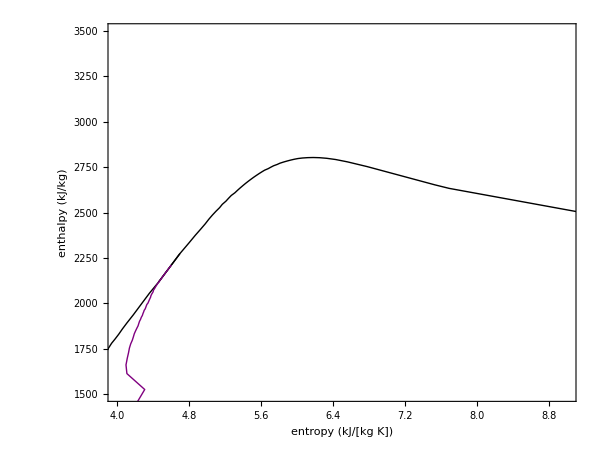

```mathematica
quality=ListPlot[qual[0.4],Joined->True,PlotStyle->{{Thick,Purple}},PlotRange->All];
Show[diagram,quality]
```

```mathematica
(*CONSTANT PRESSURE*)
```

```mathematica
P50={{0.68,252.03},{1.1,395.29},{1.49,539.43},{1.84,684.91},{2.17,832.5},{2.49,983.22},{2.79,1138.4},{3.08,1300.2},{3.37,1471.60},{3.67,1658.8},{4.,1874.4},{4.4,2145.9},{4.85,2474.8},{5.22,2758.3},{5.49,2972.8},{5.7,3145.1},{5.87,3292.9},{6.02,3425.4},{6.15,3547.9},{6.27,3663.4},{6.38,3773.9},{6.48,3880.8},{6.58,3985.1},{6.67,4087.4},{6.76,4188.2},{6.84,4288.},{6.92,4387.},{7.,4485.4}};
```

```mathematica
P25={{0.69,230.79},{1.12,375.62},{1.51,521.41},{1.87,668.86},{2.2,819.02},{2.52,973.38},{2.84,1134.2},{3.15,1305.60},{3.47,1496.4},{3.87,1741.2},{5.14,2578.6},{5.56,2868.4},{5.8,3044.6},{5.99,3184.5},{6.14,3306.5},{6.28,3418.},{6.4,3523.},{6.51,3623.6},{6.61,3721.2},{6.71,3816.7},{6.81,3910.9},{6.8900,4004.},{6.98,4096.6},{7.06,4188.8},{7.14,4280.8},{7.22,4372.7},{7.3,4464.8},{7.37,4557.}};
```

```mathematica
P10={{0.7,217.94},{1.13,363.82},{1.52,510.73},{1.88,659.53},{2.22,811.53},{2.55,968.68},{2.87,1134.3},{3.2,1315.3},{3.36,1408.10},{5.62,2725.5},{5.8,2835.8},{6.04,2981.1},{6.21,3097.4},{6.36,3200.6},{6.5,3296.5},{6.62,3388.},{6.73,3476.9},{6.83,3564.1},{6.93,3650.3},{7.03,3735.9},{7.12,3821.3},{7.21,3906.6},{7.29,3992.},{7.37,4077.7},{7.45,4163.7},{7.53,4250.1},{7.61,4337.1},{7.68,4424.5},{7.75,4512.5},{7.82,4601.1}};
```

```mathematica
P5={{0.7,213.640},{1.13,359.90},{1.52,507.19},{1.89,656.48},{2.23,809.16},{2.56,967.38},{2.88,1134.9},{2.92,1154.60},{5.97,2794.2},{6.18,2909.6},{6.36,3014.7},{6.51,3108.6},{6.65,3196.7},{6.77,3281.5},{6.8900,3364.4},{6.99,3446.3},{7.10,3527.7},{7.19,3608.8},{7.29,3690.1},{7.38,3771.5},{7.46,3853.3},{7.55,3935.6},{7.63,4018.4},{7.71,4101.8},{7.79,4185.8},{7.87,4270.4},{7.94,4355.7},{8.01,4441.7},{8.09,4528.4},{8.15,4615.8}};
```

```mathematica
P2={{0.7,211.06},{1.13,357.54},{1.53,505.08},{1.89,654.67},{2.23,807.77},{2.45,908.5},{6.34,2798.3},{6.42,2836.1},{6.60,2928.5},{6.75,3012.5},{6.8900,3092.8},{7.01,3171.},{7.13,3248.3},{7.24,3325.3},{7.35,3402.2},{7.45,3479.3},{7.55,3556.7},{7.6400,3634.7},{7.73,3713.2},{7.82,3792.4},{7.9,3872.2},{7.99,3952.8},{8.07,4034.1},{8.15,4116.1},{8.22,4198.9},{8.3,4282.5},{8.3700,4366.9},{8.44,4452.},{8.51,4537.9},{8.58,4624.6}};
```

```mathematica
P1={{0.7,210.19},{1.13,356.75},{1.53,504.38},{1.89,654.06},{2.14,762.52},{6.58,2777.1},{6.64,2803.5},{6.82,2887.},{6.97,2965.1},{7.11,3040.9},{7.23,3115.7},{7.35,3190.1},{7.47,3264.5},{7.58,3339.2},{7.68,3414.3},{7.78,3489.9},{7.87,3566.2},{7.97,3643.2},{8.06,3720.8},{8.14,3799.3},{8.23,3878.5},{8.31,3958.5},{8.39,4039.3},{8.47,4120.9},{8.55,4203.3},{8.6200,4286.5},{8.69,4370.6},{8.77,4455.4},{8.84,4541.1},{8.91,4627.5}};
```

```mathematica
P05={{0.7,209.76},{1.13,356.36},{1.53,504.02},{1.86,640.09},{6.82,2748.1},{6.84,2755.7},{7.02,2834.3},{7.17,2908.8},{7.31,2981.8},{7.44,3054.2},{7.57,3126.6},{7.68,3199.3},{7.8,3272.3},{7.9,3346.},{8.,3420.3},{8.1,3495.2},{8.2,3570.9},{8.29,3647.4},{8.38,3724.6},{8.47,3802.7},{8.55,3881.6},{8.63,3961.3},{8.71,4041.8},{8.7900,4123.2},{8.8700,4205.5},{8.94,4288.5},{9.02,4372.4},{9.09,4457.2},{9.16,4542.7},{9.23,4629.}};
```

```mathematica
P01={{0.7,209.42},{1.13,356.05},{1.3,417.5},{7.36,2674.9},{7.47,2716.6},{7.64,2786.5},{7.79,2855.7},{7.94,2924.9},{8.07,2994.4},{8.2,3064.5},{8.32,3135.1},{8.44,3206.5},{8.55,3278.6},{8.65,3351.4},{8.75,3425.},{8.85,3499.4},{8.94,3574.7},{9.04,3650.7},{9.12,3727.6},{9.21,3805.4},{9.3,3884.},{9.38,3963.5},{9.46,4043.9},{9.5400,4125.1},{9.61,4207.2},{9.69,4290.1},{9.76,4373.9},{9.83,4458.5},{9.9,4543.9},{9.97,4630.2}};
```

```mathematica
P005={{0.7,209.42},{1.13,356.05},{1.3,417.5},{7.36,2674.9},{7.47,2716.6},{7.64,2786.5},{7.79,2855.7},{7.94,2924.9},{8.07,2994.4},{8.2,3064.5},{8.32,3135.1},{8.44,3206.5},{8.55,3278.6},{8.65,3351.4},{8.75,3425.},{8.85,3499.4},{8.94,3574.7},{9.04,3650.7},{9.12,3727.6},{9.21,3805.4},{9.3,3884.},{9.38,3963.5},{9.46,4043.9},{9.54,4125.1},{9.61,4207.2},{9.69,4290.1},{9.76,4373.9},{9.83,4458.5},{9.9,4543.9},{9.97,4630.2}};
```

```mathematica
pressure=ListPlot[{P50,P25,P10,P5,P2,P1,P05,P01,P005},Joined->True,PlotStyle->{{Thick,Blue}}];
```

```mathematica
(*CONSTANT TEMPERATURE*)
```

```mathematica
T600={{28.38,3706.4},{7.47,3400},{6.12,3300},{5.5,3114.4},{5.09,2870.1},{4.77,2645}};
```

```mathematica
T500={{28.17,3489.8},{7.543826578699341,3056.88622754491},{7.14,3050},{6.49,3005},{6.11,2980.2},{5.68,2942},{5.35,2832},{5.045,2635}};
```

```mathematica
T200={{27.4,2880.1},{7.77,2880},{7.46,2870.1},{7.12,2841},{6.85,2794},{6.77,2760.}};
```

```mathematica
T100={{27.06,2688.7},{8.22,2712},{7.79,2712},{7.55,2702},{7.35,2675.6}};
```

```mathematica
T50={{26.85,2594.7},{8.74,2611},{8.45,2605},{8.2,2587}};
```

```mathematica
temperature=ListPlot[{T600,T500,T200,T100,T50},Joined->True,PlotStyle->{{Thick,RGBColor[0,0.6,0]}},PlotRange->All];
```





```mathematica
Manipulate[
Module[{cp,Plabels,Tlabels},
cp={4.407,2084.3};

Plabels=Graphics[{
Text[Rotate[Style[#1,17,Blue,Background->White],45°],{x/.Quiet@FindRoot[Interpolation[#2][x]==3100,{x,1}],3100}]&@@@{{25,P25},{10,P10},{5,P5},{2,P2},{1,P1},{0.5,P05},{0.1,P01},{0.05,P005}},
Text[Rotate[Style["50 MPa",17,Blue,Background->White],57°],{x/.Quiet@FindRoot[Interpolation[P50][x]==3250,{x,1}],3250}]
}];

Tlabels=Graphics[{
Text[Style[#1,17,RGBColor[0,0.6,0],Background->White],{8.75,Quiet@Interpolation[#2,InterpolationOrder->1][8.75]}]&@@@{{"600 °C",T600},{500,T500},{100,T100},{50,T50}}
}];

Show[diagram,
If[isobar,pressure,{}],If[isotherm,temperature,{}],
If[isobar,Plabels,{}],If[isotherm,Tlabels,{}],
Epilog->{
Text[Rotate[Style["critical point",17],55°],cp,{0,-0.75}],
{PointSize@0.02,Point@cp}
}]
],
Grid@{{
Style["show lines of constant:",Bold],
Control[{{isobar,True,Style["pressure",Blue]},{True,False}}],Spacer@10,
Control[{{isotherm,True,Style["temperature",RGBColor[0,0.6,0]]},{True,False}}]
}},
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX